# Spectral Yield Calculations

This notebook is meant to calculate the spectral yield (photons/nC) from the CBETA source and validate calculations against each other. Several methods are proposed in order to do this:
• Analytical calculations using the Serafini F_ψ flux in a collimator equation ✓ 
• C. Sun’s spectral output ✓
• Balsa’s ICCS spectral output ✓
• My personal run of ICCS ✓ Invalidated as Balsa needed to modify ICCS because of integration errors

Other benchmarking activities need to be undertaken:
• Use my improved windows version to try to reproduce Kirsten’s ODU source spectra ✓

Potential problems that have came to mind this far through benchmarking this are:
• Could C. Sun’s method have a scaling factor we are unaware of? Would explain the arbitrary units! Maybe like a factor of 100 - potentially the number of integration steps?
• The weird shape produced by ICCS and the fact that it shouts ‘integration problems’ make me think that potentially there is an effect like I saw using the adaptive integration in Mathematica. This is exactly what happened ✓
• Why does my analytical calculation give almost exactly double what you’d expect from Geoff’s rule of thumb? Corrected via ComptonCalcs

## Units + Constants

```mathematica
(*prefixes etc.*)
pC=10^-12;
μJ=10^-6;
nm=10^-9;
mm=10^-3;
ps=10^-12;
keV=10^3;
MeV=10^6;
mrad=10^-3;
μm=10^-6;
nC=10^-9;
```

```mathematica
(*constants*)
c=299792458;
me=0.51099895MeV;
hbar=6.5821*10^-16; (*hbar in eV*)
σT=6.65245871548*10^-29;
echarge=1.60217662*10^-19;
```

# Analytical Calculation Yield (Full Spectrum)

## Parameters

```mathematica
(*CBETA source parameters*)
Ee=150MeV;
λ=1064nm;
ϕ=0;
θobs=0;
Q=32pC;
Epulse=62μJ;
σze=1mm;
tpulse=10ps;
βIP=0.126;
ϵn=0.3mm mrad;
σL=25μm;
θcol=0.435mrad;
```

## Intermediaries

```mathematica
(*Scattered photon energy equations*) 
γ[Ee_]:=Ee/me;
β[Ee_]:=Sqrt[1-1/γ[Ee]^2];
EL[λ_]:=(2*π*hbar*c)/λ; (*in eV, using hbar*)
Xrec[Ee_,λ_]:=(4*γ[Ee]*EL[λ])/me;
(*Scattered Photon Energy*)
EγCSUN[λ_,Ee_,ϕ_,θobs_]:=(EL[λ]*(1-β[Ee]*Cos[π-ϕ]))/(1-β[Ee]*Cos[θobs]+EL[λ]/Ee*(1-Cos[π-ϕ-θobs]));
```

```mathematica
(*Photon production equations*)
σc[Ee_,λ_]:=σT*(1-Xrec[Ee,λ]);
Ne[Q_]:=Q/echarge;
NL[Epulse_,λ_]:=Epulse/(echarge*EL[λ]);
σe[βIP_,ϵn_,Ee_]:=Sqrt[(βIP*ϵn)/γ[Ee]];
σzl[tpulse_]:=c*tpulse;
convxy[βIP_,ϵn_,Ee_,σL_]:=Sqrt[σe[βIP,ϵn,Ee]^2+σL^2];
convz[σze_,tpulse_]:=Sqrt[σze^2+σzl[tpulse]^2];
(*No. Photons from single bunch-pulse interaction*)
Nγ[Ee_,λ_,Q_,Epulse_,ϕ_,βIP_,ϵn_,σL_,tpulse_]:=σc[Ee,λ](Ne[Q]*NL[Epulse,λ]*Cos[ϕ/2])/(2*π*convxy[βIP,ϵn,Ee,σL]*Sqrt[convxy[βIP,ϵn,Ee,σL]^2*Cos[ϕ/2]^2+convz[βIP,ϵn,Ee,tpulse]^2*Sin[ϕ/2]^2]);
```

```mathematica
(*Collimation Equations*)
ψ[Ee_,θcol_]:=γ[Ee]*θcol;
(*No. Photons from collimated single bunch-pulse interaction*)
Nψ[Ee_,λ_,Q_,Epulse_,ϕ_,βIP_,ϵn_,σL_,tpulse_,θcol_]:=Sqrt[2]/π*Nγ[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,tpulse]*((1+(CubeRoot[Xrec[Ee,λ]]*ψ[Ee,θcol]^2)/3)*ψ[Ee,θcol]^2)/((1+(1+Xrec[Ee,λ]/2)ψ[Ee,θcol]^2)*(1+ψ[Ee,θcol]^2));
```

## Purely Analytical Yield Calculations

```mathematica
(*No. Photons Uncollimated Spectrum*)
Nγ[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,tpulse]
```

929.171

```mathematica
(*Photon Yield Uncollimated Spectrum (photons/nC)*)
analyticaluncolyield[Ee_,λ_,Q_,Epulse_,ϕ_,βIP_,ϵn_,σL_,tpulse_]:=nC/Q*Nγ[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,tpulse];
```

```mathematica
analyticaluncolyield[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,tpulse]
```

29036.6

```mathematica
(*No. Photons Collimated Spectrum*)
Nψ[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,tpulse,θcol]
```

6.60772

```mathematica
(*Percentage through the collimator*)
Nψ[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,tpulse,θcol]/Nγ[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,tpulse]*100
```

0.711142

```mathematica
(*Photon Yield Collimates Spectrum (photons/nC)*)
analyticalcolyield[Ee_,λ_,Q_,Epulse_,ϕ_,βIP_,ϵn_,σL_,tpulse_,θcol_]:=nC/Q*Nψ[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,tpulse,θcol];
analyticalcolyield[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,tpulse,θcol]
```

206.491

Analytically we expect 929 photons to be produced in the uncollimated spectrum. We expect 15 photons to be produced in a 0.5% bandwidth after collimation. This means 1.5% of the produced photons survive collimation. From Geoff Krafft’s F_(0.1%)=1.5*10^-3 formula, and expecting this to scale linearly, we would expect roughly 0.75% of photons to survive - a factor of 2 difference, but a good sanity check!

# C Sun Yield Calculation

## Input of Spectral Data

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Spectrum_Data"];
```

```mathematica
CSUNCBETA=<<"CBETA150.txt";
```

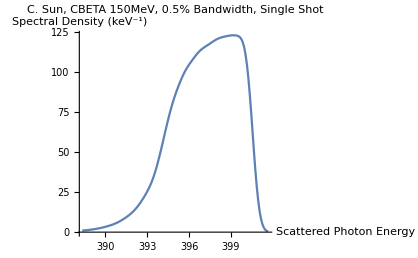

```mathematica
ListLinePlot[CSUNCBETA,AxesLabel->{"Scattered Photon Energy (keV)","Spectral Density (keV^-1)"},PlotLabel->"C. Sun, CBETA 150MeV, 0.5% Bandwidth, Single Shot"]
```

## C Sun Yield Calculation

```mathematica
(*Find the area under the curve*) 
CSUNarea=Integrate[Interpolation[CSUNCBETA][x],{x,Min[CSUNCBETA⟦All,1⟧],Max[CSUNCBETA⟦All,1⟧]}]
```

779.126

```mathematica
(*Calculate the 0.5% bandwith Energies*)
peakSun=EγCSUN[λ,Ee,ϕ,0]+0.0
```

400555.

```mathematica
Head@peakSun
```

Real

```mathematica
Sun05=EγCSUN[λ,Ee,ϕ,0]*(1-0.005)
```

398552.

```mathematica
Max[Transpose[CSUNCBETA]⟦2⟧]
```

122.881

```mathematica
peakline={{peakSun,0},{peakSun,Max[Transpose[CSUNCBETA]⟦2⟧]}}
line05=Line[{{Sun05,0},{Sun05,Max[Transpose[CSUNCBETA]⟦2⟧]}}];
```

{{400555.,0},{400555.,122.881}}

```mathematica
(*Why can't I plot my lines??*)
```

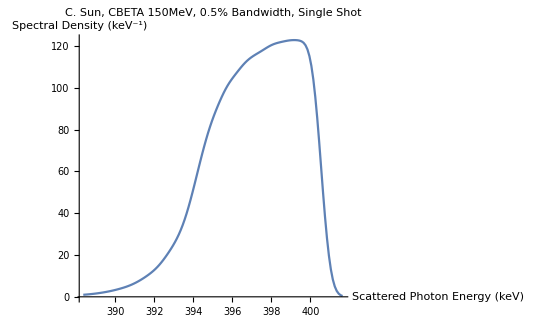

```mathematica
ListLinePlot[CSUNCBETA,AxesLabel->{"Scattered Photon Energy (keV)","Spectral Density (keV^-1)"},PlotLabel->"C. Sun, CBETA 150MeV, 0.5% Bandwidth, Single Shot",Epilog->{Line[{{IntegerPart[EγCSUN[λ,Ee,ϕ,0]],0},{IntegerPart[EγCSUN[λ,Ee,ϕ,0]],Max[Transpose[CSUNCBETA]⟦2⟧]}}]}]
```

```mathematica
Line[{{peakSun,0},{peakSun,Max[Transpose[CSUNCBETA]⟦2⟧]}}]
```

Line[{{400555.,0},{400555.,122.881}}]

```mathematica
Max[Transpose[CSUNCBETA]⟦2⟧]
```

122.881

```mathematica
(*Calculate the collimated yield (photons/nC)*)
CSUNyield=nC/Q*CSUNarea
```

24347.7

Not sure if this yield calculation is correct. Is my spectral density actually in s^-1 keV^-1? Whats the binning and actual units of this calculation - can’t make sense of it at all!

# Balsa ICCS

• Balsa has corrected the adaptive integration error in his code.

## Input of Spectral Data

```mathematica
rawdataBalsa=Import["C:/Users/user/Documents/ICCS_code/ICCS_data/output_ICCS_Balsa_new.txt","Words"] ;
```

```mathematica
ndataBalsa=Length[rawdataBalsa];
```

```mathematica
ncolumnsBalsa=4;
```

```mathematica
ndatBalsa=ndataBalsa/ncolumnsBalsa;
```

```mathematica
BalsaICCS=Array[η,{2,ndatBalsa}];
```

```mathematica
For[i=0,i<(ndatBalsa+1),i++,
(*for energy*)
η[1,i]=Interpreter["Number"][ToString[rawdataBalsa⟦1+ncolumnsBalsa*(i-1)⟧]]*10^-3;
(*for specden*)
η[2,i]=Interpreter["Number"][ToString[rawdataBalsa⟦3+ncolumnsBalsa*(i-1)⟧]];
];
```

```mathematica
(*Loop to remove zero values*)
```

```mathematica
BalsaVals=Array[τ,{2,0}];
```

```mathematica
For[i=1,i<Length[Transpose[BalsaICCS]]+1,i++,
If[BalsaNewICCS⟦2,i⟧>10^-30,
AppendTo[BalsaVals⟦1⟧,BalsaICCS⟦1,i⟧];
AppendTo[BalsaVals⟦2⟧,BalsaICCS⟦2,i⟧];
];
];
```

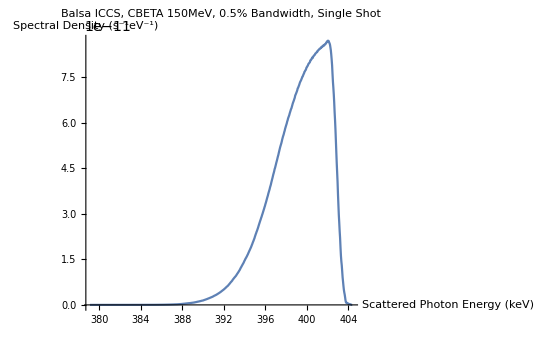

```mathematica
ListLinePlot[Transpose[BalsaVals],PlotRange->All,AxesLabel->{"Scattered Photon Energy (keV)","Spectral Density (s^-1eV^-1)"},PlotLabel->"Balsa ICCS, CBETA 150MeV, 0.5% Bandwidth, Single Shot"]
```

## ODU ICS Benchmarking

```mathematica
rawdataODU320=Import["C:/Users/user/Documents/ICCS_code/ICCS_data/output_ICCS_ODU_320g.txt","Words"] ;
rawdataODU110=Import["C:/Users/user/Documents/ICCS_code/ICCS_data/output_ICCS_ODU_110g.txt","Words"];
rawdataODU120=Import["C:/Users/user/Documents/ICCS_code/ICCS_data/output_ICCS_ODU_120g.txt","Words"];
rawdataODU140=Import["C:/Users/user/Documents/ICCS_code/ICCS_data/output_ICCS_ODU_140g.txt","Words"];
```

```mathematica
ndataODU=Length[rawdataODU320];
ncolumnsODU=3;
ndatODU=ndataODU/ncolumnsODU;
nsets=4;
```

```mathematica
ODUICCS=Array[z,{2*nsets,ndatODU}];
```

```mathematica
For[i=0,i<(ndatODU+1),i++,
(*3/20γ*)
z[1,i]=Interpreter["Number"][ToString[rawdataODU320⟦1+ncolumnsODU*(i-1)⟧]];
z[2,i]=Interpreter["Number"][ToString[rawdataODU320⟦2+ncolumnsODU*(i-1)⟧]];
(*1/10γ*)
z[3,i]=Interpreter["Number"][ToString[rawdataODU110⟦1+ncolumnsODU*(i-1)⟧]];
z[4,i]=Interpreter["Number"][ToString[rawdataODU110⟦2+ncolumnsODU*(i-1)⟧]];
(*1/20γ*)
z[5,i]=Interpreter["Number"][ToString[rawdataODU120⟦1+ncolumnsODU*(i-1)⟧]];
z[6,i]=Interpreter["Number"][ToString[rawdataODU120⟦2+ncolumnsODU*(i-1)⟧]];
(*1/40γ*)
z[7,i]=Interpreter["Number"][ToString[rawdataODU140⟦1+ncolumnsODU*(i-1)⟧]];
z[8,i]=Interpreter["Number"][ToString[rawdataODU140⟦2+ncolumnsODU*(i-1)⟧]];
];
```

```mathematica
ListLinePlot[{Partition[Riffle[ODUICCS⟦1⟧,ODUICCS⟦2⟧],2],Partition[Riffle[ODUICCS⟦3⟧,ODUICCS⟦4⟧],2],Partition[Riffle[ODUICCS⟦5⟧,ODUICCS⟦6⟧],2],Partition[Riffle[ODUICCS⟦7⟧,ODUICCS⟦8⟧],2]},PlotRange->All,AxesLabel->{"Scattered Photon Energy (keV)","Spectral Density (s^-1eV^-1)"},PlotLabel->"ODU ICS",PlotStyle->{Red,Green,Blue,Black},PlotLegends->Placed[{"θ_col=3/20γ","θ_col=1/10γ","θ_col=1/20γ","θ_col=1/40γ"},{0.2,0.6}]]
```

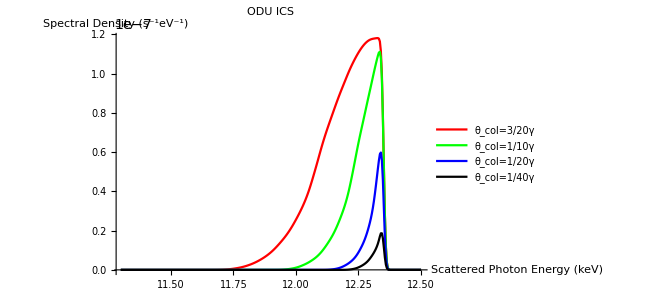
```mathematica
-Graphics--Graphics-
```

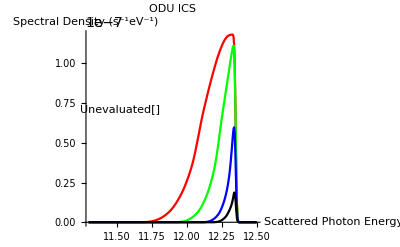

The plots look fairly identical in shape and character between my ICCS python3 version and the version used in Kirsten’s PRSTAB 12, 062801 (2016). However, the is a notable change of scale.